### V2

```mathematica
progress =Module[{sorted = SortBy[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Year&], curr, weightsovertime,improvements,locs},
Table[
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 30}]];
```

```mathematica
ListPlot[ReplacePart[#, {1-> Style[#[[1]], Red], -1-> Style[#[[-1]], ColorData[96,"ColorList"][[1]]]}]&/@ 
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress, {2}], PlotStyle->Directive[Lighter[Gray], PointSize[.0075]], Prolog->({Opacity[.3, Gray],HalfLine[{#Year,#Period},{-1,0}]&/@progress[[All, -1]]}), PlotRange->{{1969, 2025}, {2, 30}}, AspectRatio->.4, Frame-> True]
```

-Graphics-

### Trying to improve callout plot

Variable heights is a nightmare because it messes with the alignment of the year!! The only way to fix this is to stretch the plot out which will look weird.

But I got it to work, now just need to change exponent slightly for image size and image height.

```mathematica
ClearAll@place
place[currloc_, data_]:= 
Module[{size}, 
size = 2Last[Dimensions[First@CellularAutomaton["GameOfLife",{data["MatrixData"],0},data["Period"]]]];
Sow[Callout[{data["Year"] - 1969, 0}, 
Rotate[Labeled[CellularAutomatonHistoryPlot["GameOfLife", {data["MatrixData"], 0}, data["Period"], ImageSize->10size^(.5),Mesh->True,MeshStyle->Opacity[.1]], data["Year"]], -90Degree], {currloc[[1]] ,currloc[[2]]} ,LeaderSize->{{10,90 °,3}, {3,90°}}, "CalloutStyle"-> Lighter[Gray, .6]
]];
{currloc[[1]] +6size^(.4), currloc[[2]]}]
```

```mathematica
Row[Column[
Table[Module[{weightsovertime,improvements,locs,p=i},weightsovertime=Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Labeled[ListPlot[r = Reap[f = FoldList[place,{3,8},SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]]]][[2]], PlotRange->{{-10,2025 - 1969 + 30}, {-5, 15Max[Differences[f][[All, 1]]]^.55}}, Axes->None, PlotStyle->AbsolutePointSize[5], ImageSize->{250,15Max[Differences[f][[All, 1]]]^.55}, AspectRatio->Full ],Text["period "<>ToString[i]<>"  "],Left]],{i,#}],Dividers->{None,GrayLevel[.8]}, BaselinePosition->Top]&/@{Range[2,11],Range[12,21]},Spacer[10], Alignment->Top]
```

-Graphics-period 2  
-Graphics-period 3  
-Graphics-period 4  
-Graphics-period 5  
-Graphics-period 6  
-Graphics-period 7  
-Graphics-period 8  
-Graphics-period 9  
-Graphics-period 10  
-Graphics-period 11  -Graphics-period 12  
-Graphics-period 13  
-Graphics-period 14  
-Graphics-period 15  
-Graphics-period 16  
-Graphics-period 17  
-Graphics-period 18  
-Graphics-period 19  
-Graphics-period 20  
-Graphics-period 21

```mathematica
Column[Table[ListPlot[Table[{i, 5}, {i, 1, 10}], PlotRange->{{0, 11}, {0, k}}, ImageSize->{210, k}, Axes-> None, AspectRatio->Full], {k, {100, 200}}]]
```

-Graphics-

### Labeling first element of plot

```mathematica
ListLinePlot[Labeled[{Callout[1, "h"] ,2, 3}, "hi", Left]]
```

-Graphics-

```mathematica
ListLinePlot[MapIndexed[Labeled[Callout[Style[{#Year,Times@@Dimensions[#MatrixData]}],ArrayPlot[ArrayPad[#MatrixData,1],ImageSize->Tiny], LabelVisibility->Automatic]&/@#, If[Times@@Dimensions[#[[1, "MatrixData"]]] >= 1900, First[#2], None],Left]&,Table[Module[{weightsovertime,improvements,locs,p=i},weightsovertime=Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]]],{i,2,50}]],PlotStyle->PointSize[.01],PlotRange->All,AspectRatio->.4,Frame->True,FrameLabel->{None,"area"},PlotRangePadding->{{.2,.2},Automatic}]
```

InterpolatingFunction::dmval: Input value {1/120} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1/60} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1/40} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

This is not pretty...

### Larger than 30 periods

```mathematica
progress =DeleteCases[Module[{sorted = SortBy[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Year&], curr, weightsovertime,improvements,locs},
Table[
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 100}]], {}];
```

```mathematica
ListPlot[ReplacePart[#, {1-> Style[#[[1]], Red], -1-> Style[#[[-1]], ColorData[96,"ColorList"][[1]]]}]&/@ 
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress, {2}], PlotStyle->Directive[Lighter[Gray], PointSize[.01]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress[[All, -1]]}), PlotRange->{{1969, 2021}, {0, 82}}, AspectRatio->.4, Frame-> True]
```

-Graphics-

### Fixing period bug

#### Old

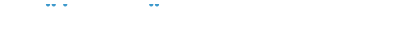
-Graphics-
-Graphics-period 2  
-Graphics-
-Graphics-period 3  
-Graphics-
-Graphics-period 4  
-Graphics-
-Graphics-period 5  
-Graphics-
-Graphics-period 6  
-Graphics-
-Graphics-period 7  
-Graphics-
-Graphics-period 8  
-Graphics-
-Graphics-period 9  
-Graphics-
-Graphics-period 10  
-Graphics-
-Graphics-period 11  
-Graphics-
-Graphics-period 12  -Graphics-
-Graphics-period 13  
-Graphics-
-Graphics-period 14  
-Graphics-
-Graphics-period 15  
-Graphics-
-Graphics-period 16  
-Graphics-
-Graphics-period 17  
-Graphics-
-Graphics-period 18  
-Graphics-
-Graphics-period 19  
-Graphics-
-Graphics-period 20  
-Graphics-period 21

```mathematica
Row[Column[Table[Module[{weightsovertime,improvements,locs,p=i, byyear},
byyear = Catenate[
ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@ 
GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&], #Year&]
];weightsovertime=Times@@Dimensions[#MatrixData]&/@byyear;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Labeled[Column[{GraphicsRow[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,ImageSize->3 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]],Mesh->True,MeshStyle->Opacity[.1]],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top]&/@byyear[[locs]]],NumberLinePlot[Callout[#Year,#Year]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]],Axes->None,PlotRange->{1968,2025}]}],Text["period "<>ToString[i]<>"  "],Left]],{i,#}],Dividers->{None,GrayLevel[.8]}]&/@{Range[2,12],Range[13,21]},Spacer[15]]
```

#### New

```mathematica
ClearAll@place
place[currloc_, data_]:= 
Module[{size}, 
size = 2Last[Dimensions[First@CellularAutomaton["GameOfLife",{data["MatrixData"],0},data["Period"]]]];
Sow[Callout[{data["Year"] - 1969, 0}, 
Rotate[Labeled[CellularAutomatonHistoryPlot["GameOfLife", {data["MatrixData"], 0}, data["Period"], ImageSize->10size^(.5),Mesh->True,MeshStyle->Opacity[.1]], data["Year"]], -90Degree], {currloc[[1]] ,currloc[[2]]} ,LeaderSize->{{10,90 °,3}, {3,90°}}, "CalloutStyle"-> Lighter[Gray, .6]
]];
{currloc[[1]] +6size^(.4), currloc[[2]]}]
```

```mathematica
Row[Column[
Table[Module[{weightsovertime,improvements,locs,p=i, byyear},
byyear = Catenate[
ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@ 
GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&], #Year&]
];
weightsovertime=Times@@Dimensions[#MatrixData]&/@byyear;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Labeled[ListPlot[r = Reap[f = FoldList[place,{3,8},byyear[[locs]]]][[2]], PlotRange->{{-10,2025 - 1969 + 30}, {-5, 15Max[Differences[f][[All, 1]]]^.55}}, Axes->None, PlotStyle->AbsolutePointSize[5], ImageSize->{250,15Max[Differences[f][[All, 1]]]^.55}, AspectRatio->Full ],Text["period "<>ToString[i]<>"  "],Left]],{i,#}],Dividers->{None,GrayLevel[.8]}, BaselinePosition->Top]&/@{Range[2,11],Range[12,21]},Spacer[10], Alignment->Top]
```

-Graphics-period 2  
-Graphics-period 3  
-Graphics-period 4  
-Graphics-period 5  
-Graphics-period 6  
-Graphics-period 7  
-Graphics-period 8  
-Graphics-period 9  
-Graphics-period 10  
-Graphics-period 11  -Graphics-period 12  
-Graphics-period 13  
-Graphics-period 14  
-Graphics-period 15  
-Graphics-period 16  
-Graphics-period 17  
-Graphics-period 18  
-Graphics-period 19  
-Graphics-period 20  
-Graphics-period 21